# Creating Figures

## Basic Exercises

### Question Subsection

Draw a human figure with circles, triangles, and rectangles. Use your imagination and get creative.

#### Solution

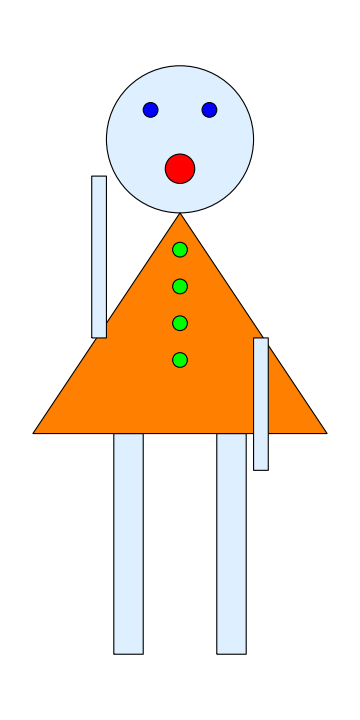

```mathematica
Graphics[{
{LightBlue,EdgeForm[{Thick,Black}],Disk[{0,10},1]},
{Blue,EdgeForm[{Thick,Black}],Disk[{-0.4,10.4},0.1]},
{Blue,EdgeForm[{Thick,Black}],Disk[{0.4,10.4},0.1]},
{Red,EdgeForm[{Thick,Black}],Disk[{0,9.6},0.2]},
{Orange,EdgeForm[{Thick,Black}],Triangle[{{0,9},{-2,6},{2,6}}]},
{Green,EdgeForm[{Thick,Black}],Disk[{0,8.5},0.1]},
{Green,EdgeForm[{Thick,Black}],Disk[{0,8},0.1]},
{Green,EdgeForm[{Thick,Black}],Disk[{0,7.5},0.1]},
{Green,EdgeForm[{Thick,Black}],Disk[{0,7},0.1]},
{LightBlue,EdgeForm[{Thick,Black}],Rectangle[{1,5.5},{1.2,7.3}]},
{LightBlue,EdgeForm[{Thick,Black}],Rectangle[{-1,7.3},{-1.2,9.5}]},
{LightBlue,EdgeForm[{Thick,Black}],Rectangle[{0.5,3},{0.9,6}]},
{LightBlue,EdgeForm[{Thick,Black}],Rectangle[{-0.5,3},{-0.9,6}]}
}]
```

### Question Subsection

The following snippet of code will import {x,y} data for the borders of Italy. Run it and then use it to plot the map of Italy.

```mathematica
italy=Import[NotebookDirectory[]<>"ItalyBorder.dat"];
```

#### Hint

Use Polygon together with Graphics.

#### Solution

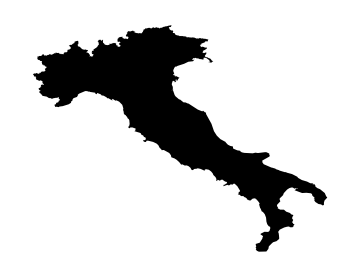

```mathematica
Graphics[Polygon[italy],ImageSize->Medium]
```

### Question Subsection

The following will import data for Italy, Germany, Spain, France, and Switzerland. Plot these countries with a light blue shading, and thick black lines for borders.

```mathematica
italy=Import[NotebookDirectory[]<>"ItalyBorder.dat"];
germany=Import[NotebookDirectory[]<>"GermanyBorder.dat"];
spain=Import[NotebookDirectory[]<>"SpainBorder.dat"];
france=Import[NotebookDirectory[]<>"FranceBorder.dat"];
switzerland=Import[NotebookDirectory[]<>"SwitzerlandBorder.dat"];
```

#### Solution

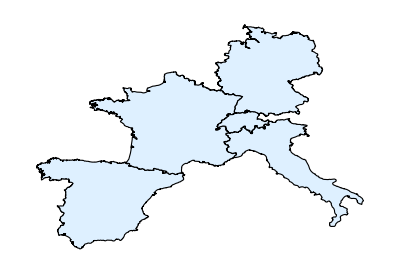

```mathematica
Graphics[{
{LightBlue,EdgeForm[{Thick,Black}],Polygon[italy]},
{LightBlue,EdgeForm[{Thick,Black}],Polygon[germany]},
{LightBlue,EdgeForm[{Thick,Black}],Polygon[spain]},
{LightBlue,EdgeForm[{Thick,Black}],Polygon[france]},
{LightBlue,EdgeForm[{Thick,Black}],Polygon[switzerland]}
}]
```

### Question Subsection

Let’s give the countries more of an identity. The following snippet defines flag colors for each country. Use these with the option VertexColors for Polygon to make each country look colorful according to their own flags.

```mathematica
germancolors={RGBColor["Black"],RGBColor["Red"],RGBColor["Yellow"]};
italiancolors={RGBColor["Green"],RGBColor["White"],RGBColor["Red"]};
frenchcolors={RGBColor["Blue"],RGBColor["White"],RGBColor["Red"]};
spanishcolors={RGBColor["Red"],RGBColor["Yellow"],RGBColor["Red"]};
swisscolors={RGBColor["Red"],RGBColor["White"],RGBColor["Red"]};
```

#### Hint

Look at the documentation to learn how to use VertexColors. 
The idea is to simply give each vertex one of the colors of the flag at random. You can use RandomChoice for this. Mathematica will interpolate the colors for the region based on the information it receives about the vertices.

#### Solution

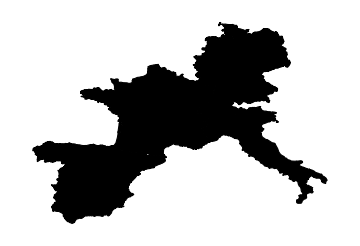

```mathematica
Graphics[{
{EdgeForm[{Thick,Black}],Polygon[italy,VertexColors->Table[RandomChoice[italiancolors],{Length[italy]}]]},
{EdgeForm[{Thick,Black}],Polygon[germany,VertexColors->Table[RandomChoice[germancolors],{Length[germany]}]]},
{EdgeForm[{Thick,Black}],Polygon[spain,VertexColors->Table[RandomChoice[spanishcolors],{Length[spain]}]]},
{EdgeForm[{Thick,Black}],Polygon[france,VertexColors->Table[RandomChoice[frenchcolors],{Length[france]}]]},
{EdgeForm[{Thick,Black}],Polygon[switzerland,VertexColors->Table[RandomChoice[swisscolors],{Length[switzerland]}]]}
},ImageSize->Medium]
```